```mathematica
mVal=0.28;
a1Val=2.2;
a2Val=4.1;
b1Val=10;
b2Val=56.6;
cVal=-0.0068;
d1Val=1.3;
d2Val=19.6;
llVal=25;

hbar=6.582119569*10^(-16) ;(* in Ev*s  *)
```

```mathematica
f[e_]:=a1^2+2*d1*(e-c)-2*b1*m
r[e_]:=f[e]^2-4*(d1^2-b1^2)*((e-c)^2-m^2)
λ1[e_]:=Sqrt[(-f[e]+Sqrt[r[e]])/(2*(d1^2-b1^2))]
λ2[e_]:=Sqrt[(-f[e]-Sqrt[r[e]])/(2*(d1^2-b1^2))]
```

```mathematica
f1=((c-m-e-(d1+b1)*λ1[e]^2)*λ2[e])/((c-m-e-(d1+b1)*λ2[e]^2)*λ1[e])-Tanh[λ1[e]*ll/2]/Tanh[λ2[e]*ll/2];
f2=((c-m-e-(d1+b1)*λ1[e]^2)*λ2[e])/((c-m-e-(d1+b1)*λ2[e]^2)*λ1[e])-Tanh[λ2[e]*ll/2]/Tanh[λ1[e]*ll/2];
ff1[ll_,e_]=f1//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};
ff2[ll_,e_]=f2//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};
```

```mathematica
Ep[ll_]:=Re[e]/.FindRoot[ff2[ll,e]==0,{e,0}]
Em[ll_]:=Re[e]/.FindRoot[ff1[ll,e]==0,{e,0}]
Delta[ll_]:=Ep[ll]-Em[ll]
E0[ll_]:=(Ep[ll]+Em[ll])/2
```

```mathematica
fp[z_,ll_,e_]:=Cosh[λ1[e]*z]/Cosh[λ1[e]*ll/2]-Cosh[λ2[e]*z]/Cosh[λ2[e]*ll/2]
fm[z_,ll_,e_]:=Sinh[λ1[e]*z]/Sinh[λ1[e]*ll/2]-Sinh[λ2[e]*z]/Sinh[λ2[e]*ll/2]
n1[ll_,e_]:=(λ1[e]^2-λ2[e]^2)/(λ1[e]*Coth[λ1[e]*ll/2]-λ2[e]*Coth[λ2[e]*ll/2])
n2[ll_,e_]:=(λ1[e]^2-λ2[e]^2)/(λ1[e]*Tanh[λ1[e]*ll/2]-λ2[e]*Tanh[λ2[e]*ll/2])
```

```mathematica
Psix=-(d1+b1)*n1[ll,e]*fm[z,ll,e];
Psiyu=I*a1*fp[z,ll,e];
Psiyd=-I*a1*fp[z,ll,e];

Chix=-(d1+b1)*n2[ll,e]*fp[z,ll,e];
Chiyu=I*a1*fm[z,ll,e];
Chiyd=-I*a1*fm[z,ll,e];
```

```mathematica
Px[z_,ll_,e_]=Psix//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};
Pyu[z_,ll_,e_]=Psiyu//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};
Pyd[z_,ll_,e_]=Psiyd//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};

Cx[z_,ll_,e_]=Chix//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};
Cyu[z_,ll_,e_]=Chiyu//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};
Cyd[z_,ll_,e_]=Chiyd//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val};
```

```mathematica
Cplus[ll_]:=1/Sqrt[Integrate[Conjugate[Px[z,ll,Ep[ll]]]*Px[z,ll,Ep[ll]]+Conjugate[Pyu[z,ll,Ep[ll]]]*Pyu[z,ll,Ep[ll]],{z,-ll/2,ll/2}]]
Cminus[ll_]:=1/Sqrt[Integrate[Conjugate[Cx[z,ll,Em[ll]]]*Cx[z,ll,Em[ll]]+Conjugate[Cyu[z,ll,Em[ll]]]*Cyu[z,ll,Em[ll]],{z,-ll/2,ll/2}]]
```

```mathematica
vFgraph[ll_]:=Im[a2Val*(10^-10)/hbar*Cminus[ll]*Cplus[ll]*Integrate[Conjugate[Px[z,ll,Ep[ll]]]*Cyd[z,ll,Em[ll]]+Conjugate[Pyu[z,ll,Ep[ll]]]*Cx[z,ll,Em[ll]],{z,-ll/2,ll/2}]]*10^(-5) 
(*Einheit dann in 10^5 m/s*)
vF[ll_]:=Im[a2Val/hbar*Cminus[ll]*Cplus[ll]*Integrate[Conjugate[Px[z,ll,Ep[ll]]]*Cyd[z,ll,Em[ll]]+Conjugate[Pyu[z,ll,Ep[ll]]]*Cx[z,ll,Em[ll]],{z,-ll/2,ll/2}]]
```

```mathematica
BB[ll_]:=Re[b2Val/2*(Cplus[ll]^2*Integrate[Conjugate[Px[z,ll,Ep[ll]]]*Px[z,ll,Ep[ll]]-Conjugate[Pyu[z,ll,Ep[ll]]]*Pyu[z,ll,Ep[ll]],{z,-ll/2,ll/2}]-Cminus[ll]^2*Integrate[Conjugate[Cx[z,ll,Em[ll]]]*Cx[z,ll,Em[ll]]-Conjugate[Cyu[z,ll,Em[ll]]]*Cyu[z,ll,Em[ll]],{z,-ll/2,ll/2}])]
DD[ll_]:=Re[b2Val/2*(Cplus[ll]^2*Integrate[Conjugate[Px[z,ll,Ep[ll]]]*Px[z,ll,Ep[ll]]-Conjugate[Pyu[z,ll,Ep[ll]]]*Pyu[z,ll,Ep[ll]],{z,-ll/2,ll/2}]+Cminus[ll]^2*Integrate[Conjugate[Cx[z,ll,Em[ll]]]*Cx[z,ll,Em[ll]]-Conjugate[Cyu[z,ll,Em[ll]]]*Cyu[z,ll,Em[ll]],{z,-ll/2,ll/2}])-d2Val]
```

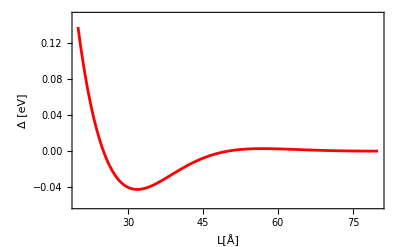

```mathematica
Plot[Delta[ll],{ll,20,80},PlotRange->{{20,80},{-0.06,0.15}},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]], Style[Row[{"Δ [eV]"}]] },PlotStyle->{Red}]
```

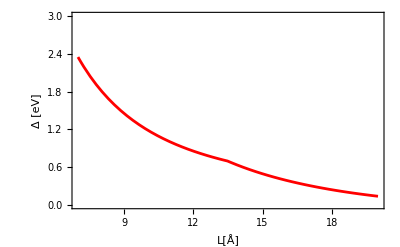

```mathematica
Plot[Delta[ll],{ll,7,20},PlotRange->{{7,20},{0,3}},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]], Style[Row[{"Δ [eV]"}]] },PlotStyle->{Red}]
```

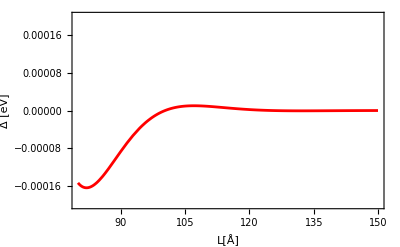

```mathematica
Plot[Delta[ll],{ll,80,150},PlotRange->{{80,150},{-0.0002,0.0002}},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]], Style[Row[{"Δ [eV]"}]] },PlotStyle->{Red}]
```

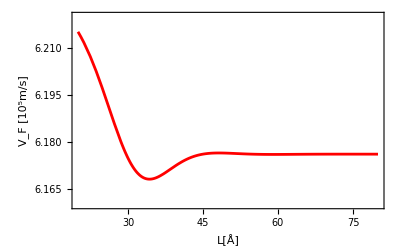

```mathematica
Plot[vFgraph[ll],{ll,20,80},PlotRange->{{20,80},{6.16,6.22}},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]], Style[Row[{Subscript["V","F"]," [",Superscript[10,5],"m/s]"}]] },PlotStyle->{Red}]
```

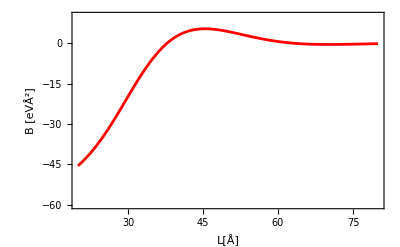

```mathematica
Plot[BB[ll],{ll,20,80},PlotRange->{{20,80},{-60,10}},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]],Style[Row[{"B [eV",Superscript["Å",2],"]"}]] },PlotStyle->{Red}]
```

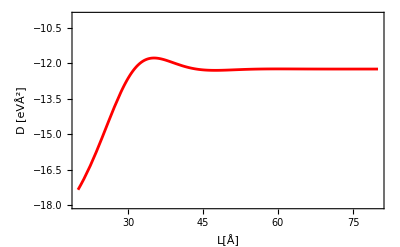

```mathematica
Plot[DD[ll],{ll,20,80},PlotRange->{{20,80},{-18,-10}},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]],  Style[Row[{"D [eV",Superscript["Å",2],"]"}]] },PlotStyle->{Red}]
```

```mathematica
DD[25]
BB[25]
```

-15.0551

-34.7615

```mathematica
TT=c+d2*k^2+d1*kz^2;
SS=c^2+2*c*d2*k^2-b2^2*k^4+d2^2*k^4+2*c*d1*kz^2-2*b1*b2*k^2*kz^2+2*d1*d2*k^2*kz^2-b1^2*kz^4+d1^2*kz^4+2*b2*k^2*m+2*b1*kz^2*m-m^2-a1^2*kz^2-a2^2*k^2;
```

```mathematica
T[kz_,k_]=TT//.{m->0.28,a1->a1Val,a2->a2Val,b1->b1Val,b2->b2Val,c->cVal,d1->d1Val,d2->d2Val};
S[kz_,k_]=SS//.{m->0.28,a1->a1Val,a2->a2Val,b1->b1Val,b2->b2Val,c->cVal,d1->d1Val,d2->d2Val};
```

```mathematica
Ebplus[kz_,k_]:=T[kz,k]+Sqrt[-S[kz,k]+T[kz,k]^2]
Ebminus[kz_,k_]:=T[kz,k]-Sqrt[-S[kz,k]+T[kz,k]^2]
```

```mathematica
kz[ll_]:=2*N[Pi,10]/ll
```

```mathematica
Ev[k_,ll_]:=E0[ll]-DD[ll]*k^2+Sqrt[(Delta[ll]/2-BB[ll]*k^2)^2+(hbar*vF[ll])^2*k^2]
Ec[k_,ll_]:=E0[ll]-DD[ll]*k^2-Sqrt[(Delta[ll]/2-BB[ll]*k^2)^2+(hbar*vF[ll])^2*k^2]
```

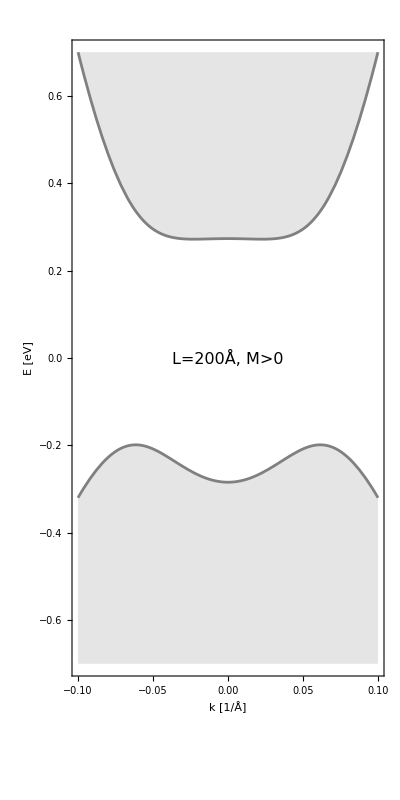

```mathematica
Plot[{Ebplus[kz[200],k],Ebminus[kz[200],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-.7,.7}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Gray,Gray},Filling->{2->Bottom,1->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=200Å, M>0",16],Scaled[{0.5,0.5}]],Axes -> False]
```

```mathematica
EwoSoc1[kz_,k_]:=cVal+d1Val*kz^2+d2Val*k^2+(+0.28-b1Val*kz^2-b2Val*k^2)
EwoSoc2[kz_,k_]:=cVal+d1Val*kz^2+d2Val*k^2-(+0.28-b1Val*kz^2-b2Val*k^2)
```

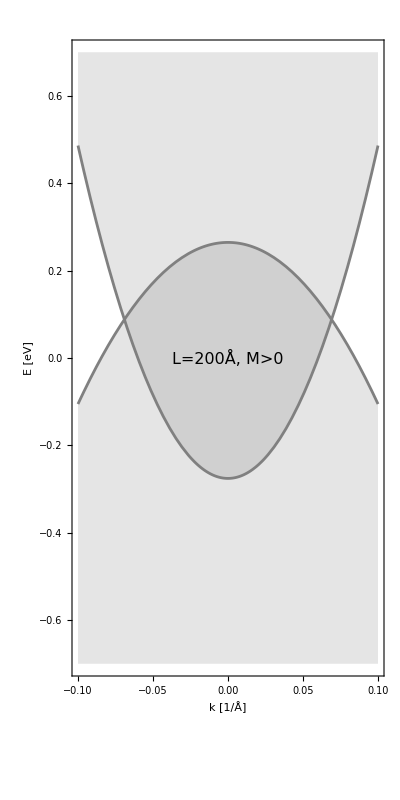

```mathematica
Plot[{EwoSoc2[kz[200],k],EwoSoc1[kz[200],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-.7,.7}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Gray,Gray},Filling->{2->Bottom,1->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=200Å, M>0",16],Scaled[{0.5,0.5}]],Axes -> False]
```

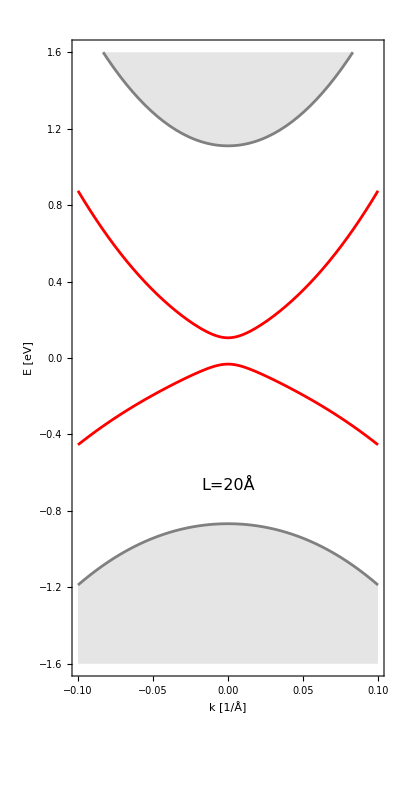

```mathematica
Plot[{Ev[k,20],Ec[k,20],Ebplus[kz[20],k],Ebminus[kz[20],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-1.6,1.6}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Red,Red,Gray,Gray},Filling->{4->Bottom,3->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=20Å",16],Scaled[{0.5,0.3}]],Axes -> False]
```

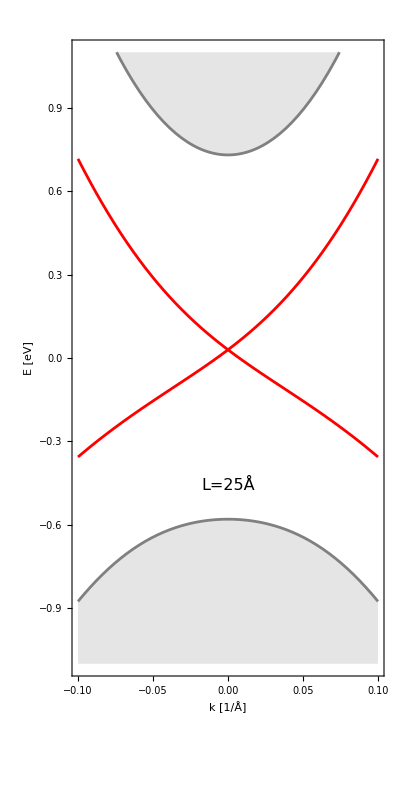

```mathematica
Plot[{Ev[k,25],Ec[k,25],Ebplus[kz[25],k],Ebminus[kz[25],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-1.1,1.1}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Red,Red,Gray,Gray},Filling->{4->Bottom,3->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=25Å",16],Scaled[{0.5,0.3}]],Axes -> False]
```

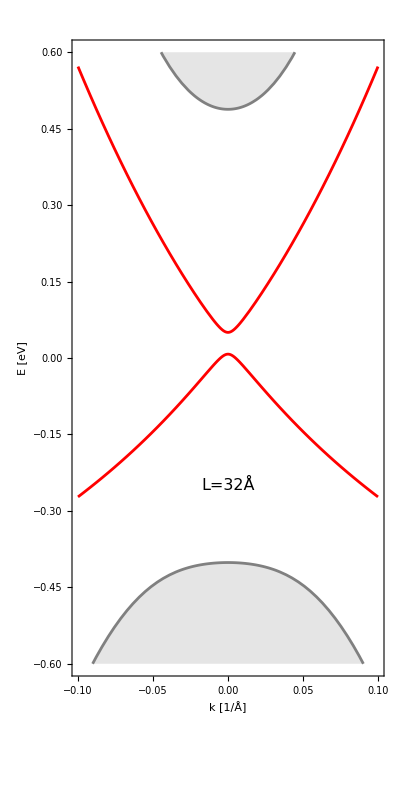

```mathematica
Plot[{Ev[k,32],Ec[k,32],Ebplus[kz[32],k],Ebminus[kz[32],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-0.6,0.6}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Red,Red,Gray,Gray},Filling->{4->Bottom,3->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=32Å",16],Scaled[{0.5,0.3}]],Axes -> False]
```

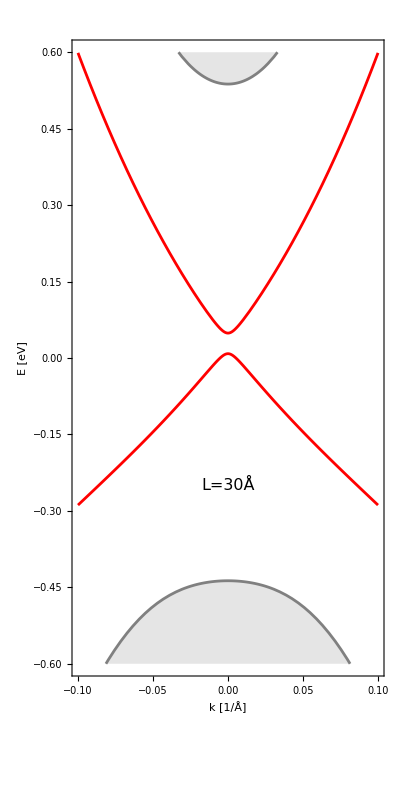

```mathematica
Plot[{Ev[k,30],Ec[k,30],Ebplus[kz[30],k],Ebminus[kz[30],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-0.6,0.6}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Red,Red,Gray,Gray},Filling->{4->Bottom,3->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=30Å",16],Scaled[{0.5,0.3}]],Axes -> False]
```

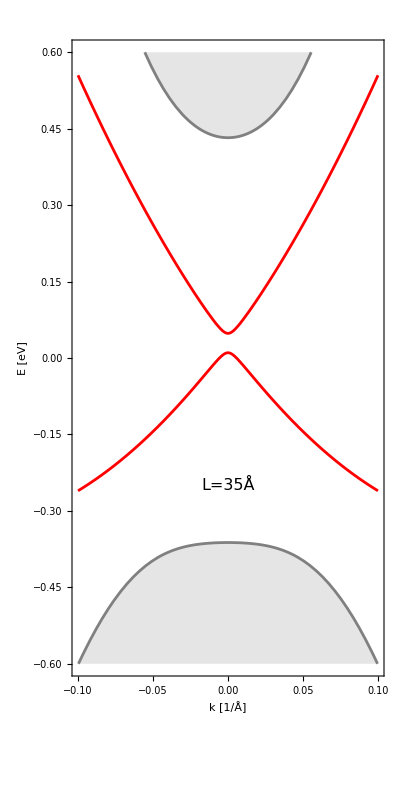

```mathematica
Plot[{Ev[k,35],Ec[k,35],Ebplus[kz[35],k],Ebminus[kz[35],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-0.6,0.6}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Red,Red,Gray,Gray},Filling->{4->Bottom,3->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=35Å",16],Scaled[{0.5,0.3}]],Axes -> False]
```

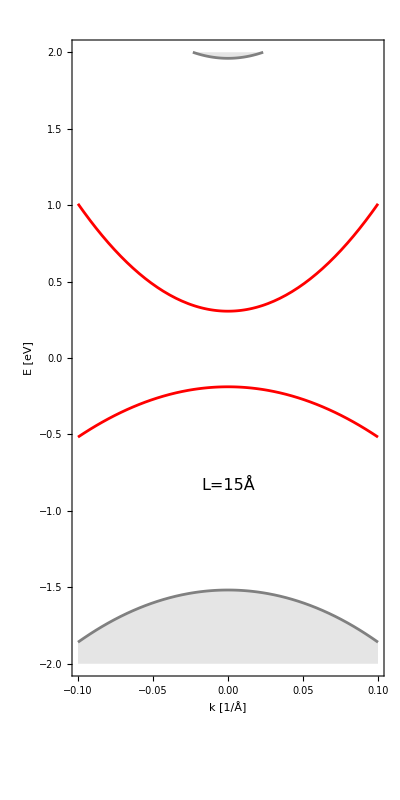

```mathematica
Plot[{Ev[k,15],Ec[k,15],Ebplus[kz[15],k],Ebminus[kz[15],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-2,2}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Red,Red,Gray,Gray},Filling->{4->Bottom,3->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=15Å",16],Scaled[{0.5,0.3}]],Axes -> False]
```

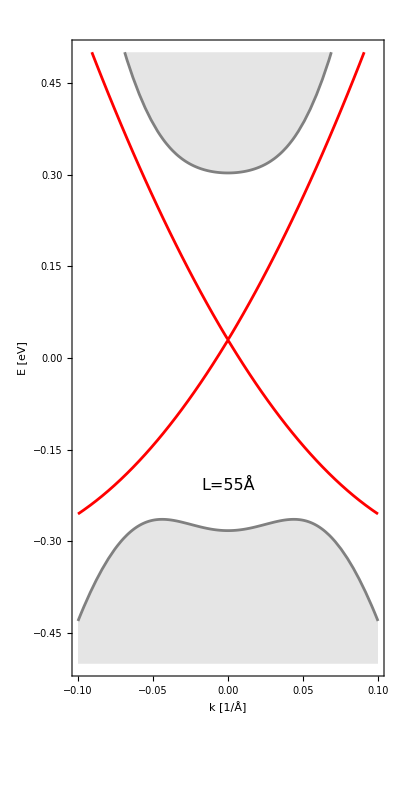

```mathematica
Plot[{Ev[k,55],Ec[k,55],Ebplus[kz[55],k],Ebminus[kz[55],k]},{k,-0.1,0.1},PlotRange->{{-0.1,0.1},{-0.5,0.5}},Frame->True, FrameLabel->{Style[Row[{"k [1/Å]"}]], Style[Row[{"E [eV]"}]] },PlotStyle->{Red,Red,Gray,Gray},Filling->{4->Bottom,3->Top},AspectRatio->2/1,ImageSize-> Scaled[0.2],Prolog->Inset[Style["L=55Å",16],Scaled[{0.5,0.3}]],Axes -> False]
```

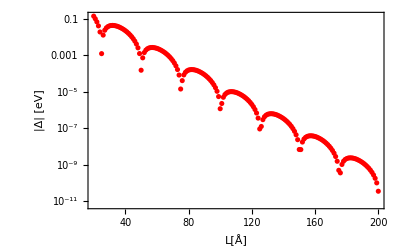

```mathematica
ListPlot[Table[{ll,Abs[Delta[ll]]},{ll,20,200,1}],ScalingFunctions->{"Linear","Log"},PlotStyle->Red,AxesLabel->{"x-Wert","y-Wert"},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]], Style[Row[{" |Δ| [eV]"}]] },PlotRange->{{20,200}, Automatic},Ticks->{Automatic,(*x-Achse bleibt automatisch*)Table[{10^(-n),Style[Superscript[10,-n],Larger]},{n,1,11}]}]
```

```mathematica
λ1[1]//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val}
```

0.+0.297564 ⅈ

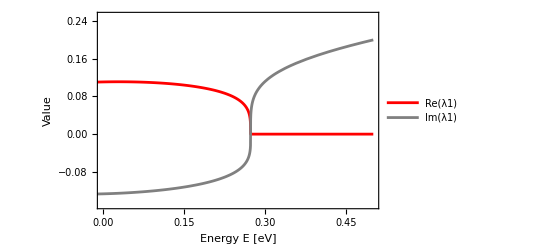

```mathematica
Plot[{Re[λ1[e]//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val}
],Im[λ1[e]//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val}
]},{e,-.50,.5},PlotStyle->{Red,Gray},Frame->True,FrameLabel->{ Style[Row[{" Energy E [eV]"}]],Style["Value"]},PlotRange->{{0,.5},{-0.15,0.25}},PlotLegends->Placed[{"Re(λ1)","Im(λ1)"},{.15,.85}]]
```

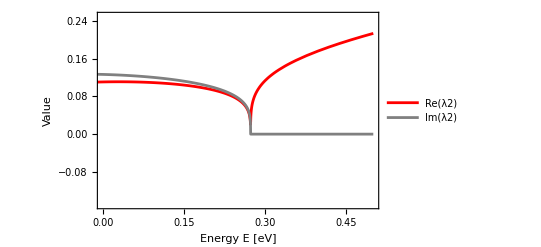

```mathematica
Plot[{Re[λ2[e]//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val}
],Im[λ2[e]//.{m->mVal,a1->a1Val,b1->b1Val,c->cVal,d1->d1Val}
]},{e,-.50,.5},PlotStyle->{Red,Gray},Frame->True,FrameLabel->{ Style[Row[{" Energy E [eV]"}]],Style["Value"]},PlotRange->{{0,.5},{-0.15,0.25}},PlotLegends->Placed[{"Re(λ2)","Im(λ2)"},{.15,.85}]]
```

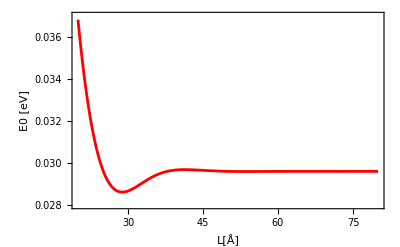

```mathematica
Plot[E0[ll],{ll,20,80},PlotRange->{{20,80},{0.028,0.037}},Frame->True, FrameLabel->{Style[Row[{"L[Å]"}]], Style[Row[{"E0 [eV]"}]] },PlotStyle->{Red}]
```

```mathematica
gg=200;
h1=Re[Cminus[gg]];
h2=Re[Cplus[gg]];
```

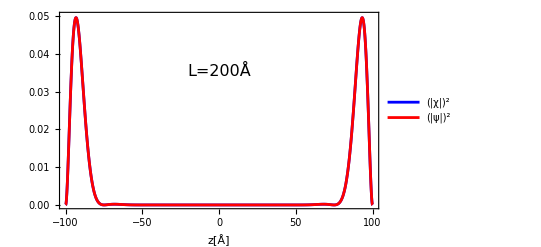

```mathematica
Plot[{h1^2*(Conjugate[Cx[z,gg,Em[gg]]]*Cx[z,gg,Em[gg]]+Conjugate[Cyu[z,gg,Em[gg]]]*Cyu[z,gg,Em[gg]]),h2^2*(Conjugate[Px[z,gg,Ep[gg]]]*Px[z,gg,Ep[gg]]+Conjugate[Pyu[z,gg,Ep[gg]]]*Pyu[z,gg,Ep[gg]])},{z,-gg/2,gg/2},PlotRange->{{-gg/2,gg/2},{0,0.05}},Frame->True, FrameLabel->{Style[Row[{"z[Å]"}]],  Style[Row[{}]] },PlotStyle->{Blue,Red},Prolog->Inset[Style["L=200Å",16],Scaled[{0.5,0.7}]],Axes->False,PlotLegends->Placed[{Superscript["|χ|",2],Superscript["|ψ|",2]},{.5,.4}]]
```

## Spin konfiguration

```mathematica
lll=20;
DeDe=Delta[lll];
BeBe=BB[lll];
vFvF=vF[lll];
DeDe
BeBe
```

0.137888

-45.4828

```mathematica
ϵc[kx_,ky_]:=-Sqrt[(DeDe/2-BeBe*(kx^2+ky^2))^2+(hbar*vFvF)^2*(kx^2+ky^2)]
ϵv[kx_,ky_]:=Sqrt[(DeDe/2-BeBe*(kx^2+ky^2))^2+(hbar*vFvF)^2*(kx^2+ky^2)]
Nc[kx_,ky_,tz_]:=1/Sqrt[(tz*(DeDe/2-BeBe*(kx^2+ky^2))+ϵc[kx,ky])^2+(hbar*vFvF)^2*(kx^2+ky^2)]
Nv[kx_,ky_,tz_]:=1/Sqrt[(tz*(DeDe/2-BeBe*(kx^2+ky^2))+ϵv[kx,ky])^2+(hbar*vFvF)^2*(kx^2+ky^2)]
ac[kx_,ky_,tz_]:=tz*(DeDe/2-BeBe*(kx^2+ky^2))+ϵc[kx,ky]
av[kx_,ky_,tz_]:=tz*(DeDe/2-BeBe*(kx^2+ky^2))+ϵv[kx,ky]
EWxc[kx_,ky_,tz_]:=Nc[kx,ky,tz]^2*ac[kx,ky,tz]*2*hbar*vFvF*ky
EWxv[kx_,ky_,tz_]:=Nv[kx,ky,tz]^2*av[kx,ky,tz]*2*hbar*vFvF*ky
EWyc[kx_,ky_,tz_]:=-Nc[kx,ky,tz]^2*ac[kx,ky,tz]*2*hbar*vFvF*kx
EWyv[kx_,ky_,tz_]:=-Nv[kx,ky,tz]^2*av[kx,ky,tz]*2*hbar*vFvF*kx
EWzc[kx_,ky_,tz_]:=Nc[kx,ky,tz]^2*(ac[kx,ky,tz]^2-(hbar*vFvF)^2*(kx^2+ky^2))
EWzv[kx_,ky_,tz_]:=Nv[kx,ky,tz]^2*(av[kx,ky,tz]^2-(hbar*vFvF)^2*(kx^2+ky^2))
plot1=VectorPlot3D[{EWxv[kx,ky,-1],EWyv[kx,ky,-1],EWzv[kx,ky,-1]},{kx,-.10,.10},{ky,-.10,.10},{kz,-0.1,0.1},Axes->True,VectorStyle->"Arrow3D",VectorPoints->8,RegionFunction->Function[{x,y,z},-0.01<z<0.01],Boxed->True, Background->None, PlotRangePadding->None,BoxRatios->{1,1,1/10},PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.01,0.01}},Ticks->{Automatic,Automatic,None}];
plot2=VectorPlot3D[{EWxc[kx,ky,-1],EWyc[kx,ky,-1],EWzc[kx,ky,-1]},{kx,-.10,.10},{ky,-.10,.10},{kz,-0.1,0.1},Axes->True,VectorStyle->"Arrow3D",VectorPoints->8,RegionFunction->Function[{x,y,z},-0.01<z<0.01],Boxed->True, Background->None, PlotRangePadding->None,BoxRatios->{1,1,1/10},PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.01,0.01}},Ticks->{Automatic,Automatic,None}];
```

```mathematica
GraphicsGrid[{{plot1},{plot2}}]
```

-Graphics-